## Importing data and functions

TimeImpacts imports results of 1000 impacts on brachiating gait family under time-based switching. StateImpacts imports the same, under state-based switching. BUone is the initial brachiating gait family, containing time-based switching eigenvalues. StateBUone contains the same, under state-based switching. Indices corresponding to changes in stability are defined for time-based and state-based switching.

```mathematica
SetDirectory[NotebookDirectory[]];
<< "TwoLink`"
TimeImpacts=Import["TimeImpactsBUone.wxf"];
StateImpacts = Import["StateImpactsBUone.wxf"];
Get["TimeBranches.m"];
Get["StateBUone.m"];
BUone=Flatten[Lookup[branches,{"bu⟦1⟧-","bu⟦1⟧+"}],1];
Needs["MaTeX`"];
DefaultPhysicalParameters[];
CompileFunctions[];
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"BranchImpacts.nb"}],InsertResults->False,EvaluationElements->"InitializationCell"];
firstStableIdxTime=7584;
lastStableIdxTime=8616;
firstStablePtTime=TimeImpacts[[firstStableIdxTime,1]];
lastStablePtTime=TimeImpacts[[lastStableIdxTime,1]];
firstStableIdxState=163;
lastStableIdxState=2736;
radToDeg=180./Pi;
```

## Figure 2 right subfigure

Simulates example brachiating gate under time-based and state-based switching. Depicts the difference in the convergence of these two switching strategies.

```mathematica
initialConds={0.4311684275169334,2.356012670075704,-0.07933342559141594,0.1339786342941721,2.1714254065174696};

stateSim=NImpactSimulationStateSwitching[initialConds];
timeSim=NImpactSimulationTimeSwitching[initialConds];

stateCoords=stateSim[[-6;;,{5,6}]];
timeCoords=timeSim[[-8;;,{5,6}]];
stateCoords[[All,2]]*=radToDeg;
timeCoords[[All,2]]*=radToDeg;

ptState=stateCoords[[1]];
ptTime=timeCoords[[6]];

xlab=MaTeX["\\tau",FontSize->30];
ylab=MaTeX["\\sigma",FontSize->30];
xticks={#,MaTeX[ToString[#],FontSize->20]}&/@Range[1.4,3,0.2];
yticks={#,MaTeX[ToString[Chop[#]]<>"^\\circ",FontSize->20]}&/@Range[-30,20,10];

offsetCurve={0.00006,-0.00020,0.00016,-0.00008,0.00024,-0.00036,0.00048,0.00039}*2000;
sequenceCurves=Table[{Dashed,Black,BezierCurve[{timeCoords[[i]],{timeCoords[[i,1]]+offsetCurve[[i]],(timeCoords[[i,2]]+timeCoords[[i-1,2]])/2},timeCoords[[i-1]]}]},{i,Length[timeCoords],2,-1}];

labelState=MaTeX["\\text{State-Based}",FontSize->18];
labelTime=MaTeX["\\text{Time-Based}",FontSize->18];
offsetState={0.0,-5};
offsetTime={0.00005,6};

zoomRegion={{2.15,2.2},{-18,-16.2}};

zoomPlot=ListPlot[{stateCoords,timeCoords},PlotStyle->{Directive[Blue,PointSize[1.0]],Directive[RGBColor[0,0.8,1],PointSize[0.06]]},PlotRange->zoomRegion,Frame->True,Axes->False,FrameTicks->None,ImageSize->{120,90},Background->White,ImagePadding->0,PlotRangePadding->0,Prolog->{sequenceCurves,Thick,Line[{ptState,ptState+offsetState}],Text[Framed[labelState,Background->White,FrameStyle->Black],ptState+offsetState],Thick,Line[{ptTime,ptTime+offsetTime}],Text[Framed[labelTime,Background->White,FrameStyle->Black],ptTime+offsetTime]}];

ListPlot[{stateCoords,timeCoords},PlotStyle->{Directive[Blue,PointSize[0.03]],Directive[RGBColor[0,0.8,1],PointSize[0.022]]},PlotRange->{{1.67,2.75},{-30,32}},ImageSize->500,Frame->True,AspectRatio->1.05,Background->None,FrameStyle->Black,Axes->False,FrameTicks->{{yticks,None},{xticks,None}},FrameLabel->{xlab,ylab},Prolog->{sequenceCurves,Thick,Line[{ptState,ptState+offsetState}],Text[Framed[labelState,Background->White,FrameStyle->Black],ptState+offsetState],Thick,Line[{ptTime,ptTime+offsetTime}],Text[Framed[labelTime,Background->White,FrameStyle->Black],ptTime+offsetTime]},Epilog->{{EdgeForm[{Gray,Dashed,Thickness[0.004]}],FaceForm[None],Rectangle[{zoomRegion[[1,1]],zoomRegion[[2,1]]},{zoomRegion[[1,2]],zoomRegion[[2,2]]}]},Thickness[0.002],Line[{{2.14,-18.5},Scaled[{0.35,0.14}]}],Inset[zoomPlot,Scaled[{0.2,0.15}],Center,Scaled[{0.35,0.2}]]}]
```

-Graphics-

## Figure 2 Left Subfigure

Plots two symmetric gait families projected onto the q1(0)-q2(0) plane under time-based switching. Plots unstable gaits in red and stable gaits in blue. Arrows show evolution of select gaits, converging onto the mirrored family. Bifurcation points are labeled one gait family. The seed value used to generate the gait family is visualized in the bottom right corner of the plot. A figure of the two link model is imported and displayed in the upper left corner of the plot.

```mathematica
negatedBranches=MapAt[-#&,BUone,{All,1,1;;4}];
combinedData=Join[BUone,negatedBranches];
stablePoints=Select[combinedData,Max[Abs[#[[3]]]]<1&];
unstablePoints=Select[combinedData,Max[Abs[#[[3]]]]>=1&];

stableCoords=#[[1,1;;2]]*radToDeg&/@stablePoints;
unstableCoords=#[[1,1;;2]]*radToDeg&/@unstablePoints;

seed={0.5822502168192503,1.9770922199512926,0,0,2.4506884121336117};
baseDrawing=Draw[seed[[1;;4]],(0&),{0,seed[[-1]]}];
{imgW,imgH}=ImageDimensions[baseDrawing];
seedDrawing=Show[ImageTrim[baseDrawing,{{0,0},{imgW,imgH*0.65}}],ImageSize->Full];

importedFig=First[Import[FileNameJoin[{NotebookDirectory[],"two_link_model.pdf"}],{"PDF","PageGraphics"}]];

arrowIndices={9295,9632,10020};
arrowsEpilog=Arrow[{TimeImpacts[[#,1,{1,2}]]*radToDeg,TimeImpacts[[#,-1,{1,2}]]*radToDeg}]&/@arrowIndices;

ptNS=firstStablePtTime[[{1,2}]]*radToDeg;
labelNS=MaTeX["\\text{NS}",FontSize->18];
posNS=ptNS+{-15.0,-15.0};

ptFD=lastStablePtTime[[{1,2}]]*radToDeg;
labelFD=MaTeX["\\text{FD}",FontSize->18];
posFD=ptFD+{15.0,15.0};

xlab=MaTeX["q_1(0)",FontSize->30];
ylab=MaTeX["q_2(0)",FontSize->30];
xticks={#,MaTeX[ToString[#]<>"^\\circ",FontSize->20]}&/@Range[-200,200,50];
yticks={#,MaTeX[ToString[#]<>"^\\circ",FontSize->20]}&/@Range[-200,200,50];

ListPlot[{unstableCoords,stableCoords},PlotStyle->{Directive[Red,PointSize[Small]],Directive[Blue,Thick,PointSize[Large]]},ImageSize->800,Background->None,Frame->True,FrameStyle->Black,FrameTicks->{{yticks,None},{xticks,None}},FrameLabel->{xlab,ylab},Prolog->{Directive[Gray,Dashed,Thick],Arrowheads[Medium],Arrow[{{56,-60},seed[[{1,2}]]*radToDeg}]},Epilog->{Inset[importedFig,Scaled[{0.25,0.75}],Center,Scaled[0.47]],Inset[Framed[seedDrawing,FrameStyle->Directive[Gray,Thickness[4]],FrameMargins->0],Scaled[{0.82,0.185}],Center,Scaled[0.33]],Black,Thick,Line[{ptNS,posNS}],Text[Framed[labelNS,Background->White,FrameStyle->Black],posNS],Line[{ptFD,posFD}],Text[Framed[labelFD,Background->White,FrameStyle->Black],posFD],Arrowheads[Medium],arrowsEpilog}]
```

-Graphics-

## Figure 4 Upper Right Subfigure

Visualization of the Neimark-Sacker bifurcation found in the brachiating gait family under time-based switching. Again, unstable points are red and stable points are blue. The last 50 gaits of are plotted for a few unstable initial gaits. Invariant curves formed by these gaits are connected for visual clarity.

```mathematica
idxStart=7470;
idxEnd=7680;
stepSize=7;

dataGroups=Table[TimeImpacts[[i,-50;;,{5,1,2}]],{i,idxStart-10,firstStableIdxTime,stepSize}];
dataGroups[[All,All,2;;3]]*=radToDeg;

initialPoints=Table[TimeImpacts[[i,1,{5,1,2}]],{i,idxStart-10,firstStableIdxTime,stepSize}];
initialPoints[[All,2;;3]]*=radToDeg;

sortedGroups=Function[group,Module[{cx,cy,sorted},cx=Mean[group[[All,2]]];
cy=Mean[group[[All,3]]];
sorted=SortBy[group,ArcTan[#[[2]]-cx,#[[3]]-cy]&];
Append[sorted,First[sorted]]]]/@dataGroups;

nGroups=Length[sortedGroups];
ringStyles=Table[Directive[Blend[{Darker[Blue],RGBColor[0,0.5,1],Lighter[Blue,0.8]},N[i/nGroups]],Thickness[0.005]],{i,nGroups}];

plotRings3D=ListLinePlot3D[sortedGroups,PlotStyle->Evaluate[ringStyles]];
plotPts3D=ListPointPlot3D[initialPoints,PlotStyle->Directive[Red,PointSize[0.01]]];

lineDataStable=TimeImpacts[[firstStableIdxTime;;idxEnd,1,{5,1,2}]];
lineDataPre=TimeImpacts[[idxStart;;firstStableIdxTime,1,{5,1,2}]];
lineDataStable[[All,2;;3]]*=radToDeg;
lineDataPre[[All,2;;3]]*=radToDeg;

plotLineStable=ListLinePlot3D[lineDataStable,PlotStyle->Directive[Blue,Thickness[0.003]]];
plotLinePre=ListLinePlot3D[lineDataPre,PlotStyle->Directive[Red,Thickness[0.003]]];

Make3DCallout[point3D_,offset_,text_,color_:Black]:={color,Thickness[0.002],Line[{point3D,point3D+offset}],Text[Framed[text,Background->White,FrameStyle->Black,FrameMargins->Medium,RoundingRadius->0],point3D+offset]};

ptTarget=firstStablePtTime[[{5,1,2}]];
ptTarget[[2;;3]]*=radToDeg;
labelNS3D=MaTeX["\\text{NS}",FontSize->28];
callout3D=Graphics3D[Make3DCallout[ptTarget,{0,0,-7},labelNS3D,Black]];

xlab=MaTeX["\\tau",FontSize->30];
ylab=MaTeX["q_1",FontSize->30];
zlab=MaTeX["q_2",FontSize->30];
xticks={#,MaTeX[ToString[#],FontSize->20]}&/@Range[2.1,2.4,0.02];
yticks={#,MaTeX[ToString[#]<>"^\\circ",FontSize->20]}&/@Range[-10,50,60];
zticks={#,MaTeX[ToString[#]<>"^\\circ",FontSize->20]}&/@Range[110,150,10];

Show[plotLineStable,plotLinePre,plotRings3D,plotPts3D,callout3D,PlotRange->{{2.13,2.2},{-15,60},{115,150}},ImageSize->800,PlotLegends->None,BoxStyle->Black,Background->None,AxesEdge->{{1,1},{1,-1},{-1,1}},AxesLabel->{xlab,ylab,zlab},Ticks->{xticks,yticks,zticks},BoxRatios->{2,2.3,1}]
```

-Graphics3D-

## Figure 5 Lower Right Subfigure

Depicts the evolution of an unstable initial gait(red point) during Neimark-Sacker bifurcation. Closed invariant curve is plotted on q1-q2 plane. First 520 gaits are plotted in purple.

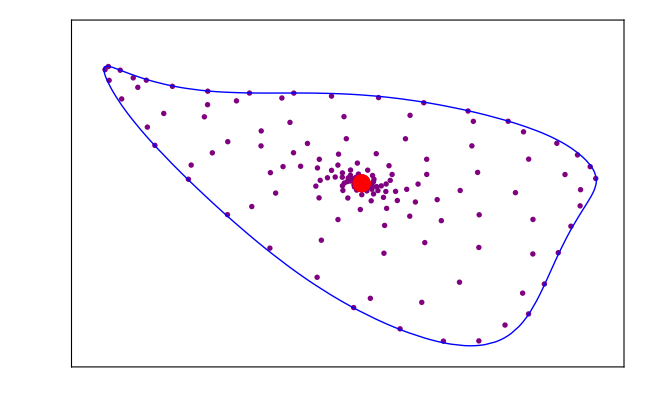

```mathematica
idx=7509;
ringPts=TimeImpacts[[idx,-300;;,{1,2}]]*radToDeg;
cx=Mean[ringPts[[All,1]]];
cy=Mean[ringPts[[All,2]]];

sortedRingPts=SortBy[ringPts,ArcTan[#[[1]]-cx,#[[2]]-cy]&];
closedRingPts=Append[sortedRingPts,First[sortedRingPts]];
edgeLine=Graphics[{Blue,Thick,Line[closedRingPts]}];

initialPtPlot=ListPlot[{TimeImpacts[[idxSection,1,{1,2}]]*radToDeg},PlotStyle->Directive[Red,PointSize[0.02]]];
sequencePtsPlot=ListPlot[TimeImpacts[[idxSection,1;;520,{1,2}]]*radToDeg,PlotStyle->Directive[Purple,PointSize[0.006]]];

xlab=MaTeX["q_1",FontSize->36];
ylab=MaTeX["q_2",FontSize->36];
xticks={#,MaTeX[ToString[#]<>"^\\circ",FontSize->24]}&/@Range[-20,80,15];
yticks={#,MaTeX[ToString[#]<>"^\\circ",FontSize->24]}&/@Range[100,180,10];

Show[sequencePtsPlot,edgeLine,initialPtPlot,Background->None,ImageSize->650,PlotRange->{{-10,55},{120,150}},Frame->True,Axes->False,FrameTicks->{{yticks,None},{xticks,None}},FrameLabel->{xlab,ylab}]
```

## Figure 4 Lower Middle Subfigure

Plotting eigenvalues during Neimark-Sacker bifurcation of the brachiating gait family under time-based switching.

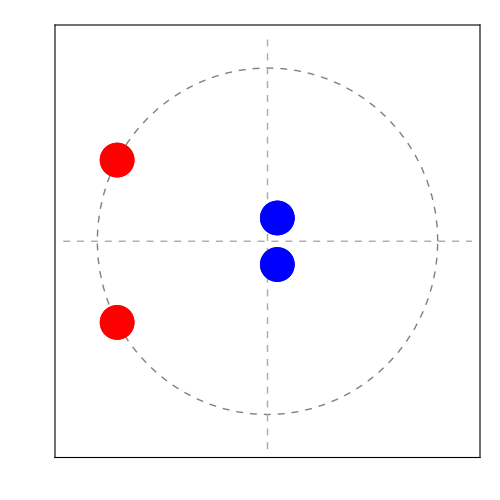

```mathematica
eigenVals=BUone[[firstStableIdxTime,3,1;;4]];
eigenPts=ReIm/@eigenVals;

prBound=1.2;
xlab=MaTeX["\\text{Im}(\\lambda)",FontSize->36];
ylab=MaTeX["\\text{Re}(\\lambda)",FontSize->36];
xticks={#,MaTeX[ToString[#],FontSize->24]}&/@Range[-1.5,1.5,0.5];
yticks={#,MaTeX[ToString[#],FontSize->24]}&/@Range[-1.5,1.5,0.5];

ListPlot[List/@eigenPts,ImageSize->500,Background->None,AspectRatio->Automatic,PlotRange->{{-prBound,prBound},{-prBound,prBound}},PlotStyle->{Directive[Red,PointSize[0.05]],Directive[Red,PointSize[0.05]],Directive[Blue,PointSize[0.05]],Directive[Blue,PointSize[0.05]]},Prolog->{Thick,Gray,Dashed,Circle[{0,0},1],Thin,Lighter[Gray],Line[{{-prBound,0},{prBound,0}}],Line[{{0,-prBound},{0,prBound}}]},Frame->True,FrameStyle->Black,FrameTicks->{{yticks,None},{xticks,None}},FrameLabel->{xlab,ylab}]
```

## Figure 4 Upper Left Subfigure

Depicts period-doubling bifurcation of the brachiating gait family under state-based switching. Initial gaits are shown in red while the last 50 gaits are shown in blue.

```mathematica
idxStart=9800;
idxEnd=10492;
pdSubset=StateImpacts[[idxStart;;idxEnd]];

scatterData=Map[Take[#[[All,{6,1}]]*radToDeg,-Min[50,Length[#]]]&,pdSubset];
lineData=SortBy[pdSubset[[All,1,{6,1}]]*radToDeg,First];

plotScatter=ListPlot[scatterData,PlotStyle->Blue];
plotLine=ListLinePlot[lineData,PlotStyle->Directive[Red,Thick]];

ptPD=(pdSubset[[All,-1,{6,1}]]*radToDeg)[[179]];
labelPD=MaTeX["\\text{PD}",FontSize->28];
posPD=ptPD+{0.5,2.0};

xlab=MaTeX["\\sigma",FontSize->30];
ylab=MaTeX["q_1",FontSize->30];
xticks={#,MaTeX[ToString[#]<>"^\\circ",FontSize->24]}&/@Range[-30,-22,1];
yticks={#,MaTeX[ToString[#]<>"^\\circ",FontSize->24]}&/@Range[78,95,3];

Show[plotLine,plotScatter,PlotRange->{{Automatic,-23.2},Automatic},ImageSize->700,Frame->True,FrameStyle->Black,FrameTicks->{{yticks,None},{xticks,None}},FrameLabel->{xlab,ylab},Epilog->{Thick,Line[{ptPD,posPD}],Text[Framed[labelPD,Background->White,FrameStyle->Black],posPD],AbsolutePointSize[8],Point[ptPD]}]
```

-Graphics-

## Figure 4 Lower Left Subfigure

Plotting eigenvalues during period-doubling bifurcation of the brachiating gait family under state-based switching.

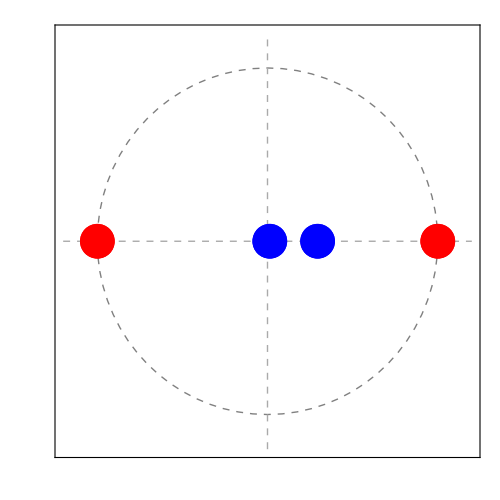

```mathematica
eigenVals=StateBUone[[lastStableIdxState,3,1;;4]];
eigenPts=ReIm/@eigenVals;

prBound=1.2;
xlab=MaTeX["\\text{Im}(\\lambda)",FontSize->36];
ylab=MaTeX["\\text{Re}(\\lambda)",FontSize->36];
xticks={#,MaTeX[ToString[#],FontSize->24]}&/@Range[-1.5,1.5,0.5];
yticks={#,MaTeX[ToString[#],FontSize->24]}&/@Range[-1.5,1.5,0.5];

ListPlot[List/@eigenPts,ImageSize->500,Background->None,AspectRatio->Automatic,PlotRange->{{-prBound,prBound},{-prBound,prBound}},PlotStyle->{Directive[Red,PointSize[0.05]],Directive[Red,PointSize[0.05]],Directive[Blue,PointSize[0.05]],Directive[Blue,PointSize[0.05]]},Prolog->{Thick,Gray,Dashed,Circle[{0,0},1],Thin,Lighter[Gray],Line[{{-prBound,0},{prBound,0}}],Line[{{0,-prBound},{0,prBound}}]},Frame->True,FrameStyle->Black,FrameTicks->{{yticks,None},{xticks,None}},FrameLabel->{xlab,ylab}]
```

## Figure 5

Initial gaits for time-based brachiating gait family and its mirrored counterpart are plotted in light colors, red being unstable and blue being stable. Select initial gaits are shown as red points. The convergence of these initial gaits are plotted as cyan points. Arrows connect a few initial and convergent gaits.

```mathematica
idxStart=9000;
idxEnd=10100;
extraIndices={10150,10200,10250,10300,10350};

extractCoords=Map[{#[[1]],#[[2]]*radToDeg}&];

bifData1=extractCoords[Flatten[TimeImpacts[[idxStart;;idxEnd,-2;;,{-2,1}]],1]];
bifData2=extractCoords[Flatten[TimeImpacts[[extraIndices,-50;;,{-2,1}]],1]];

initPts1=extractCoords[TimeImpacts[[idxStart;;idxEnd,1,{-2,1}]]];
initPts2=extractCoords[TimeImpacts[[extraIndices,1,{-2,1}]]];
finalPts1=extractCoords[TimeImpacts[[idxStart;;idxEnd,-1,{-2,1}]]];

selectedIdx={1,300,600,Length[initPts1]};
labelsABCD=Style[MaTeX["\\text{"<>#<>"}",FontSize->20],FontSize->20]&/@{"A","B","C","D"};

calloutsInit=Table[Callout[initPts1[[selectedIdx[[i]]]],labelsABCD[[i]],Above,Background->White,Frame->True,RoundingRadius->25],{i,4}];
calloutsFinal=Table[Callout[finalPts1[[selectedIdx[[i]]]],labelsABCD[[i]],Below,Background->White,Frame->True,RoundingRadius->25],{i,4}];

ptFD=extractCoords[{TimeImpacts[[8618,1,{-2,1}]]}][[1]];
labelFD=MaTeX["\\text{FD}",FontSize->24];

ptNS=extractCoords[{firstStablePtTime[[{-2,1}]]}][[1]];
labelNS=MaTeX["\\text{NS}",FontSize->24];

ptETop=extractCoords[{TimeImpacts[[10250,1,{-2,1}]]}][[1]];
ptEMid=extractCoords[{TimeImpacts[[10250,-2,{-2,1}]]}][[1]];
ptEBot=extractCoords[{TimeImpacts[[10250,-1,{-2,1}]]}][[1]];
labelE=Style[MaTeX["\\text{E}",FontSize->20],FontSize->20];
calloutsE={Callout[ptETop,labelE,Above,Background->White,Frame->True,RoundingRadius->25],Callout[ptEBot,labelE,Below,Background->White,Frame->True,RoundingRadius->25]};

qCoords=TimeImpacts[[All,All,{1,2}]]*radToDeg;
curveTau=TimeImpacts[[All,1,5]];
curveQ=qCoords[[All,1]];

curveSegments=Flatten[Table[With[{stability=Max[Abs[BUone[[j,3]]]]},{If[stability<1,Lighter[Blue,0.6],Lighter[Red,0.7]],Line[{{curveTau[[j]],curveQ[[j,1]]},{curveTau[[j]],curveQ[[j+1,1]]}}],Line[{{curveTau[[j]],-curveQ[[j,1]]},{curveTau[[j]],-curveQ[[j+1,1]]}}]}],{j,1,Length[curveQ]-1}],1];

curveLayer=Graphics[{Thickness[0.013],curveSegments}];
step=15;
dataLayer=ListPlot[{bifData1[[1;;-1;;step]],bifData2,calloutsInit,calloutsFinal,calloutsE},PlotStyle->{Directive[PointSize[0.007],Cyan],Directive[PointSize[0.007],Cyan]},PlotRange->{{1.85,2.25},{-60,100}}];

xlab=MaTeX["\\tau",FontSize->30];
ylab=MaTeX["q_1",FontSize->30];
xticks={#,MaTeX[ToString[#],FontSize->20]}&/@Range[1.85,2.2,0.1];
yticks={#,MaTeX[ToString[#]<>"^\\circ",FontSize->20]}&/@Range[-100,150,50];

Show[curveLayer,dataLayer,Frame->True,FrameStyle->Black,Axes->False,Background->None,AspectRatio->0.3,ImageSize->800,PlotRange->{{1.85,2.2},{-85,135}},PlotRangeClipping->True,FrameTicks->{{yticks,None},{xticks,None}},FrameLabel->{xlab,ylab},Epilog->{Red,PointSize[0.007],Point[initPts1[[1;;-1;;step]]],Point[initPts2],Black,Thick,Arrowheads[0.03],Table[Arrow[{initPts1[[selectedIdx[[i]]]],finalPts1[[selectedIdx[[i]]]]}],{i,4}],Thickness[0.002],Line[{ptFD,ptFD+{-0.02,0}}],Text[Framed[labelFD,Background->White,FrameStyle->Black],ptFD+{-0.02,0}],Line[{ptNS,ptNS+{0,-60}}],Text[Framed[labelNS,Background->White,FrameStyle->Black],ptNS+{0,-60},{0,1}],Thick,Arrow[{ptETop,ptEMid+{0,1}}]}]
```

-Graphics-